```mathematica
Quit[]
```

## Set Notebook Directory

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Krzysztof\Desktop\Magisterka\Praca-magisterska\Maxim-muon-scattering

## Create qList

```mathematica
(*Define a function for logarithmic spacing*)
LogSpace[start_,end_,n_]:=Exp[Subdivide[Log[start],Log[end],n-1]]

(*Use the function to generate 200 points from 1e-4 to 20.0*)
qList=LogSpace[1*10^-4,20.0,200];

(*output the qList*)
(*qList*)
```

## Read data: ma_distributions_mu_scattering.dat

```mathematica
(*Step 1:Import the CSV file*)
data=Import["ma_distributions_mu_scattering.dat","CSV"];
(*******************************************************************************************)
(*Skip the header row and extract the first element from each subsequent row: there will be fa value*)
maList=data[[2;;,1]];

(*Output the list of first elements without the header*)
maList
maList[[119]]
(*******************************************************************************************)
(*Separate header and data*)
header=data[[1]];                 (*Extract the header row*)
dataWithoutHeader=data[[2;;]];   (*Extract the data without the header row*)

(*Skip the first element in each data row*)
distributionsQPow2=Rest/@dataWithoutHeader;
(*Output the processed data without header, `f(q) * q^2*)
(*distributionsQPow2[[1]]*)
(*Here we have to divide each elelemt by q^2, `f(q)`*)
distributions = Map[MapThread[Times,{#,qList^-2}]&,distributionsQPow2];
(* f(q) * q^3*)
distributionsQPow3 = Map[MapThread[Times,{#,qList}]&,distributionsQPow2];
```

{6.2302×10^-9,6.08768×10^-9,5.94842×10^-9,5.81234×10^-9,5.67938×10^-9,5.54946×10^-9,5.42251×10^-9,5.29847×10^-9,5.17726×10^-9,5.05883×10^-9,4.9431×10^-9,4.83002×10^-9,4.71953×10^-9,4.61157×10^-9,4.50608×10^-9,4.403×10^-9,4.30227×10^-9,4.20385×10^-9,4.10769×10^-9,4.01372×10^-9,3.9219×10^-9,3.83219×10^-9,3.74452×10^-9,3.65886×10^-9,3.57516×10^-9,3.49338×10^-9,3.41347×10^-9,3.33538×10^-9,3.25908×10^-9,3.18453×10^-9,3.11168×10^-9,3.04049×10^-9,2.97094×10^-9,2.90298×10^-9,2.83657×10^-9,2.77168×10^-9,2.70828×10^-9,2.64632×10^-9,2.58579×10^-9,2.52663×10^-9,2.46883×10^-9,2.41236×10^-9,2.35717×10^-9,2.30325×10^-9,2.25056×10^-9,2.19908×10^-9,2.14877×10^-9,2.09962×10^-9,2.05159×10^-9,2.00466×10^-9,1.9588×10^-9,1.91399×10^-9,1.8702×10^-9,1.82742×10^-9,1.78562×10^-9,1.74477×10^-9,1.70486×10^-9,1.66586×10^-9,1.62775×10^-9,1.59051×10^-9,1.55413×10^-9,1.51858×10^-9,1.48384×10^-9,1.44989×10^-9,1.41673×10^-9,1.38432×10^-9,1.35265×10^-9,1.32171×10^-9,1.29147×10^-9,1.26193×10^-9,1.23306×10^-9,1.20485×10^-9,1.17729×10^-9,1.15036×10^-9,1.12404×10^-9,1.09833×10^-9,1.07321×10^-9,1.04866×10^-9,1.02467×10^-9,1.00123×10^-9,9.78322×10^-10,9.55942×10^-10,9.34074×10^-10,9.12706×10^-10,8.91828×10^-10,8.71426×10^-10,8.51492×10^-10,8.32013×10^-10,8.1298×10^-10,7.94382×10^-10,7.7621×10^-10,7.58454×10^-10,7.41104×10^-10,7.2415×10^-10,7.07585×10^-10,6.91398×10^-10,6.75582×10^-10,6.60127×10^-10,6.45026×10^-10,6.30271×10^-10,6.15853×10^-10,6.01765×10^-10,5.87999×10^-10,5.74548×10^-10,5.61404×10^-10,5.48562×10^-10,5.36013×10^-10,5.23751×10^-10,5.1177×10^-10,5.00063×10^-10,4.88624×10^-10,4.77446×10^-10,4.66524×10^-10,4.55852×10^-10,4.45424×10^-10,4.35234×10^-10,4.25278×10^-10,4.15549×10^-10,4.06043×10^-10,3.96755×10^-10,3.87679×10^-10,3.7881×10^-10,3.70145×10^-10,3.61677×10^-10,3.53403×10^-10,3.45319×10^-10,3.3742×10^-10,3.29701×10^-10,3.22159×10^-10,3.14789×10^-10,3.07588×10^-10,3.00552×10^-10,2.93676×10^-10,2.86958×10^-10,2.80394×10^-10,2.7398×10^-10,2.67712×10^-10,2.61588×10^-10,2.55604×10^-10,2.49757×10^-10,2.44043×10^-10,2.38461×10^-10,2.33006×10^-10,2.27675×10^-10,2.22467×10^-10,2.17378×10^-10,2.12405×10^-10,2.07546×10^-10,2.02799×10^-10,1.98159×10^-10,1.93626×10^-10,1.89197×10^-10,1.84869×10^-10,1.8064×10^-10,1.76508×10^-10,1.7247×10^-10,1.68524×10^-10,1.64669×10^-10,1.60902×10^-10,1.57222×10^-10,1.53625×10^-10,1.50111×10^-10,1.46677×10^-10,1.43321×10^-10,1.40043×10^-10,1.36839×10^-10,1.33709×10^-10,1.3065×10^-10,1.27661×10^-10,1.24741×10^-10,1.21888×10^-10,1.19099×10^-10,1.16375×10^-10,1.13713×10^-10,1.11111×10^-10,1.0857×10^-10,1.06086×10^-10,1.03659×10^-10,1.01288×10^-10,9.89708×10^-11,9.67067×10^-11,9.44945×10^-11,9.23329×10^-11,9.02207×10^-11,8.81568×10^-11,8.61401×10^-11,8.41696×10^-11,8.22441×10^-11,8.03627×10^-11,7.85244×10^-11,7.67281×10^-11,7.49728×10^-11,7.32578×10^-11,7.15819×10^-11,6.99444×10^-11,6.83444×10^-11,6.6781×10^-11,6.52533×10^-11,6.37606×10^-11,6.2302×10^-11}

4.06043×10^-10

## Draw row distribution

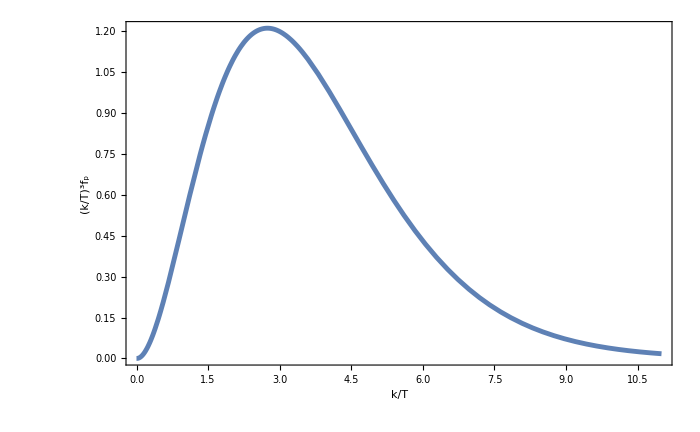

```mathematica
(*Helpfull function to create Transposed data, remeber that `i` will refer to vale of `f_a` in `faList`.*)
transposeData[i_,list_,listOfLists_List]:=Transpose[{list,listOfLists[[i]]}]
(*Create the plot*)
AxDistFunctionTab=transposeData[1,qList,distributionsQPow3]; (* f(q)*q^3 *)
AxDistFunction=Interpolation[AxDistFunctionTab,Method->"Spline",InterpolationOrder->3];
Plot[{AxDistFunction[x]},{x,0,11},Frame->True,FrameLabel->{{"(k/T)^3f_p",None},{"k/T",None}},LabelStyle->22,FrameStyle->Directive[Black,Thick],PlotStyle->{{Thickness[0.005],ColorData[97,1]},{Dashed,Thickness[0.005],ColorData[97,1]},{Thickness[0.005],Orange,ColorData[97,2]}},ImageSize-> 700]
```

## Axion distribution function : find their fit

best fit parameters: {A→0.847305,b→0.69709,μ→0.382191}[]

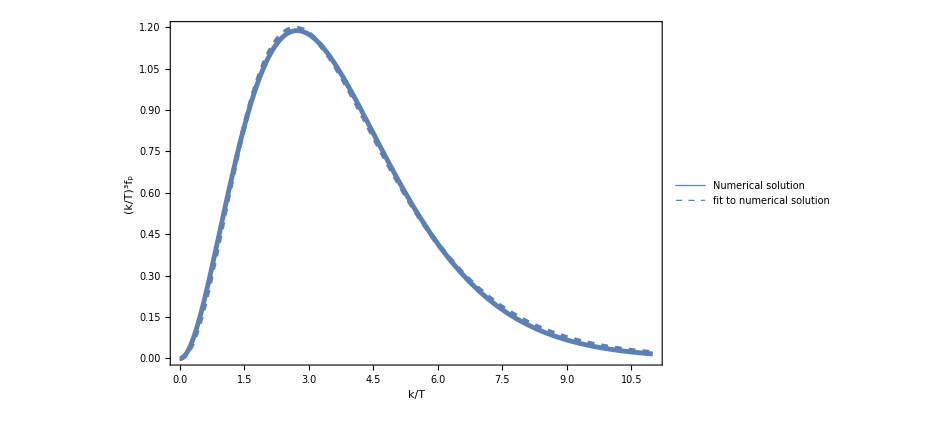

```mathematica
(*Set distrubution*)
AxDistFunctionTab=transposeData[10,qList,distributionsQPow3]; (* f(q)*q^3 *)
AxDistFunction=Interpolation[AxDistFunctionTab,Method->"Spline",InterpolationOrder->3];
(*Defined the approx axion distribution function*)
(*fApprox[x_,A_,b_,μ_]:=x^3*A(1/(Exp[x/b + μ]-1))*)
fApprox[x_,A_,b_,μ_]:=x^2(Exp[A √(1+x^2)-b]+μ)^-1

(********** Step 1: Settings to make a fit **********)
xmin = 0.0;
xmax = 11;
step = 0.005;
dataToFit=Table[{x,AxDistFunction[x]},{x,xmin,xmax,step}];
(********** Step 2: Perform the nonlinear fit **********)
fit=NonlinearModelFit[dataToFit,{fApprox[x,A,b,μ]},{A,b,μ},x,
Method->{"NMinimize",Method->{"RandomSearch","SearchPoints"->100}}];
(********** Step 3: Optional information **********)
(*Extract best-fit parameters*)
bestFitParams=fit["BestFitParameters"];
Print["best fit parameters:"bestFitParams[]];
(*Visualize the fit*)
(*Show[ListPlot[data],Plot[fit[x],{x,xmin,xmax},PlotStyle->Red]]*)

(********** Step 4: Plot distribution and fit **********)
Plot[{AxDistFunction[x], fit[x]},{x,0,11},Frame->True,FrameLabel->{{"(k/T)^3f_p",None},{"k/T",None}},LabelStyle->22,FrameStyle->Directive[Black,Thick],PlotStyle->{{Thickness[0.005],ColorData[97,1]},{Dashed,Thickness[0.005],ColorData[97,1]},{Thickness[0.005],Orange,ColorData[97,2]}},

PlotLegends->{"Numerical solution","fit to numerical solution"},
ImageSize-> 700]
```